# Boltzmann equations by Patricio Escalona Contreras

## Parameter values

### masses

```mathematica
MP=1.2209*10^19 (*2.4*10^18*);
mψ=500;
ms=200;
mh=125;
mW=80;
mZ=90;
mt=173;
mb=5;
```

### couplings and vev

```mathematica
gψ=1;
λhs=0.1;
vev=246;
```

### degrees of freedom

```mathematica
g=100;
gs=100;
```

### Higgs branching ratio

```mathematica
Γh=2*10^-3;
```

Comments:
1: Maybe we should use a “Block” command....

## λ_abcd=[(s(x=1))/(H(x=1))]σv_abcd

### Useful definitions:

```mathematica
μ=(ms mψ)/(ms +mψ);
prefactor=(2 π^2 gs μ^3)/45/((1.66 √g μ^2)/MP);
```

Comments: 
1: we will use the “time” variable x =μ/T; where μ is the reduced mass of the DM system.
2: the prefactor is the entropy over the Hubble parameter .
3: gs and g are effective degrees of freedom for entropy and energy. We will consider these as constants around 100.
4: MP is the reduced Planck Mass.

### σv_abcd for processes with dark matter as a final state:

```mathematica
σvψψsh=(gψ^2 λhs^2 vev^2 √(-2 mh^2(ms^2+4 mψ^2)+mh^4+(ms^2-4 mψ^2)^2))/(64π mψ^2(4 mψ^2-ms^2)^2)(**1.16*10^-17*)
σvψsψh=-(gψ^2 λhs^2 vev^2 √((ms^2-mh^2)((ms+2mψ)^2-mh^2))(2mψ-(-mh^2+ms^2+2ms mψ+2 mψ^2)/(ms+mψ)))/(32 π ms(ms+mψ)^2(mψ(-mh^2+ms^2+2ms mψ+2 mψ^2)/(ms+mψ)+ms^2-2 mψ^2)^2)(**1.16*10^-17*)
σvψψss=(gψ^4 mψ(mψ^2-ms^2)^(5/2))/(24 π(ms^2-2 mψ^2)^4)6 μ/mψ(*(6μ)/mψ*) (*1.16*10^-17//N*)
```

1.23195×10^-11

1.20918×10^-10

(63 √21)/(17909824000 π)

Comments: 
1: all the processes have an s-wave dominance, except for  ψ+ψ -> s+s, with dominant term in the p-wave, i.e, in v^2. We just put the coefficient here! We will put the dependence explicitly in the Boltzmann equations, (terms proportional to x^-3 in contrast to terms proportional to x^-2).
2: we always refer to thermal averaged quantities, i.e, v^2 refers to <v^2> and so on.
3: gψ is the dark Yukawa coupling, λhs is the HIggs-scalar dark matter quartic coupling

### σv_abcd for processes with standard particles as a final state:

#### Breit-Wigner expansion

```mathematica
Dh2=1/((s-mh^2)^2+mh^2 Γh^2);
```

Comments:
1: Γh is the Higgs branching ratio, approx. 2 MeV (Why? this quantity depends on the energy of the DM annihilation processes? )

#### σv_abcd for electroweak gauge bosons and heaviest quarks final states

```mathematica
σvssWW=(λhs^2 s)/(8 π)√(1-4 mW^2/s)Dh2(1-4 mW^2/s+12(mW^2/s)^2);
σvssZZ=(λhs^2 s)/(8 π)1/2 √(1-4 mZ^2/s)Dh2(1-4 mZ^2/s+12(mZ^2/s)^2);
σvsstt=(λhs^2 mt^2)/(4 π)3(√(1-4 mt^2/s))^3 Dh2;
σvssbb=(λhs^2 mb^2)/(4 π)3(√(1-4 mb^2/s))^3 Dh2;
```

Comments:
1: We should include a 1-loop QCD correction.

#### σv_abcd for higgs boson final states

```mathematica
vs=√(1-(4 ms^2)/s);
vh=√(1-(4 mh^2)/s);
aR=1+3 mh^2(s-mh^2)Dh2;
aI=3 mh^2 √s Γh Dh2;
tminus=ms^2+mh^2-1/2 s(1+vs vh); 
tplus= ms^2+mh^2-1/2 s(1-vs vh);
σvsshh=λhs^2/(16 π s^2 vs)((aR^2+aI^2)s vs vh +(2 λhs^2 vev^4 s vs vh)/((ms^2-tminus)(ms^2-tplus)));
```

Comments:
2: Just a lot of notation extracted explicitly from the reference.
1: We will use this quantity in the non-relativistic limit, i.e √s-> 2 ms. But this quantity diverges in such a limit. So we use a slightly different number with no numerical consequence as far as we know. We suspect that is just a Mathematica notation issue. This is the only process with this issue.
2: Maybe I should use also the p-wave contribution, which we suspect have a relevance comparable with the p dominant term ψψ->ss. 
									(I GUESS that is s -> 4 ms^2 +4 v^2 or something alike)

### λ_abcd

```mathematica
λψψsh=prefactor*σvψψsh
λψsψh=prefactor*σvψsψh
λψψss=prefactor*σvψψss
λssXX=prefactor*(σvssWW+σvssZZ+σvsstt+σvssbb+σvsshh)
```

5.67785×10^10

5.57289×10^11

2.36483×10^13

4.60884×10^21 ((71.4502 (1-119716/s)^(3/2))/(1/16+(-15625+s)^2)+(0.0596831 (1-100/s)^(3/2))/(1/16+(-15625+s)^2)+(0.000198944 √(1-32400/s) (1+787320000/s^2-32400/s) s)/(1/16+(-15625+s)^2)+(0.000397887 √(1-25600/s) (1+491520000/s^2-25600/s) s)/(1/16+(-15625+s)^2)+1/(√(1-160000/s) s^2)0.000198944 ((7.32437×10^7 √(1-160000/s) √(1-62500/s) s)/((-15625+1/2 (1-√(1-160000/s) √(1-62500/s)) s) (-15625+1/2 (1+√(1-160000/s) √(1-62500/s)) s))+√(1-160000/s) √(1-62500/s) s ((1+(46875 (-15625+s))/(1/16+(-15625+s)^2))^2+(140625 s)/(16 (1/16+(-15625+s)^2)^2))))

### Numerical values

```mathematica
Block[{gs=100,gψ=0.1,MP=10^18,ms=300,mψ=500,mh=125,vev=256,λhs=0.1,g=100},{λψψsh,λψsψh,λψψss}]
```

{5.67785×10^10,5.57289×10^11,2.36483×10^13}

```mathematica
Block[{gs=100,gψ=0.1,MP=10^18,ms=300,mψ=500,mh=125,vev=256,λhs=0.1,g=100,mt=173,mb=5,mW=80,mZ=90,s=4 ms^2+0.0000001,Γh=2*10^-3},{λssXX}]
```

{2.62284×10^13}

Comments:
1: Just to see some numerical sample. Note that the value 10^12 is always present, and is a relevant scale.
2: Note the presence of the “slightly different number” (see previous  section comment 2)
3: All is in GeV units

## Equilibrium abundances: Y_e=n_e/s

```mathematica
yψe[x_]=N[10^12(45 mψ^2 x^2 BesselK[2,(mψ x)/μ])/(2 gs π^4 μ^2)];
yse[x_]=N[10^12(45 ms^2 x^2 BesselK[2,(ms x)/μ])/(4 gs π^4 μ^2)];
```

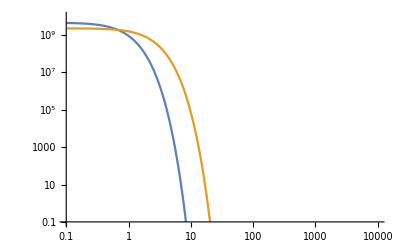

```mathematica
ploteq=LogLogPlot[{yψe[x],yse[x]},{x,0.1,10000},PlotRange->{{0.1,10000},{0.1,10^10}}]
```

Comments: 
1: We have seen this functions as something like x^(3/2)e^-x . The Bessel function is equivalent.
2: n is the number density. s is the entropy density.
3: We use this functions to “factor out” the expansion of the Universe.
4: the 10^12 factor is introduced for numerical issues (see Solving Boltzmann equations/Normalization section comments )

## Solving Boltzmann equations

### Normalization

```mathematica
λψψssnew=λψψss/10^12
λψψshnew=λψψsh/10^12
λψsψhnew=λψsψh/10^12
λssXXnew=λssXX/10^12/.s->4 ms^2+0.0001
```

23.6483

0.0567785

0.557289

26.2284

Comments:
1: In solving the equation, Mathematica use a very small diference between two big numbers. So we normalize in order to improve the 
efficiency of the program. 
2: Again, note the presence of the the “+ 0.001” quantity.

### Finally, the solutions

```mathematica
Sol=NDSolveValue[{yψ'[x]==-x^-3 λψψssnew((yψ[x])^2-(ys[x])^2(yψe[x])^2/(yse[x])^2)-x^-2 λψψshnew((yψ[x])^2-ys[x](yψe[x])^2/yse[x]),
ys'[x]==-x^-2 λssXXnew((ys[x])^2-(yse[x])^2)+x^-3 λψψssnew((yψ[x])^2-(ys[x])^2(yψe[x])^2/(yse[x])^2)+1/2 x^-2 λψψshnew((yψ[x])^2-ys[x](yψe[x])^2/yse[x])-1/2 x^-2 λψsψhnew(ys[x]*yψ[x]-yψ[x]*yse[x]),yψ[1]==yψe[1],ys[1]==yse[1]},{yψ[x],ys[x]},{x,1,10000},Method->{"StiffnessSwitching"},MaxSteps->10^6,WorkingPrecision->20]
```

NDSolveValue::precw: The precision of the differential equation ({{yψ'[x]==-(0.0567785 (-3.53695×10^11 Power[«2»] Power[«2»] Power[«2»] ys[«1»]+yψ[«1»]^2))/x^2-(23.6483 (-156.25 Power[«2»] Power[«2»] Power[«2»]+yψ[«1»]^2))/x^3,ys'[x]==-(26.2284 (-5.12411×10^18 Power[«2»] Power[«2»]+(«1»)^2))/x^2-(0.278645 («1»))/x^2+(«21» («1»))/x^2+(23.6483 («1»))/x^3,yψ[1]==«21»,ys[1]==1.58906×10^9},{},{},{},{}}) is less than WorkingPrecision (20.).

{InterpolatingFunction[…][x],InterpolatingFunction[…][x]}

```mathematica
plot=LogLogPlot[Sol,{x,1,10000},
PlotRange->{{0.1,10000},{0.1,10^10}}];
```

Comments:
1: what about this code problem?!?!? Is relevant? I mean, the plots are good-looking!
2: Note that two terms in the first equation are proportional to x^-3. This is because we extract the x dependence (see σvψψss comment)

## Plot

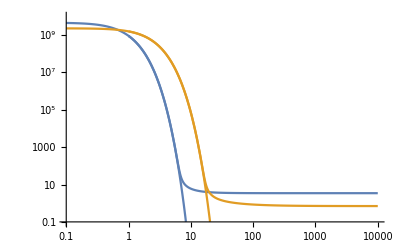

```mathematica
Show[plot,ploteq]
```

Comments:
1: Remember; we have to take care of normalization: y=10^12 Y.

## Comparation

```mathematica
Yψ0=InterpolatingFunction[…][10^4]/10^12
Ys0=InterpolatingFunction[…][10^4]/10^12
```

3.44685×10^-12

7.03886×10^-13

```mathematica
gs0=3.91;(*grados de libertad de entropia hoy, Baumann Cap3*)
kb=8.617*10^-14;(*cte de boltzmann, GeV/K, Wikipedia*)
h=0.7;
T0=0.24*10^-12;(*temperatura hoy, GeV, Baumann Cap3*)
s0=(2 π^2)/45 gs0 (T0)^3;(*entropia hoy*)
ρc=8.0992 h^2 *10^-47 ;(*densidad critica, GeV^-4*)
Ωψ=(mψ*s0*Yψ0)/ρc;
Ωs=(ms*s0*Ys0)/ρc;
Ωψ*(0.7)^2
Ωs*(0.7)^2
```

0.504519

0.0412115

CASI LOS DE BASTIAN. SERA EL METODO DE RESOLUCION? VER DETALLES 28/01/2021

```mathematica
Yψ[x_]=Sol[[1]]/10^12;
Ys[x_]=Sol[[2]]/10^12;
Yψ[10^4]
Ys[10^4]
```

3.446849560324195559×10^-12

7.038862542923139434×10^-13